```mathematica
<<~/Desktop/Software/CRunDec3/RunDec.m
```

RunDec: a Mathematica package for running and decoupling of the

strong coupling and quark masses

by K.G. Chetyrkin, J.H. K\"uhn and M. Steinhauser (January 2000)

by F. Herren and M. Steinhauser (February 2017, v3.0)

## Plot Cross Section, (up to 5000 GeV)

```mathematica
α=1/137.04;
Conversion=389379;
n=3;
Subscript[C, F]=(n^2-1)/(2n);
Born=(4π α^2)/(3s);
```

```mathematica
As[Q_]:=AsRunDec[asMz/.NumDef,Mz/.NumDef,Q^2,2];
σ[Q_]:=Conversion*(4π α^2)/(3Q*Q)(1+(3As[Q])/(4π)Subscript[C, F])
```

```mathematica
Qmax=5000.;
Qmin=1.;
Npt=500;
Q[i_]:=(Qmax-Qmin)/Npt*i+Qmin
```

```mathematica
TableCross=Table[{Q[i],σ[Q[i]]},{i,0,Npt}]
```

{{1.,99.4606},{10.998,0.743913},{20.996,0.203067},{30.994,0.0929671},{40.992,0.0530693},{50.99,0.0342623},{60.988,0.0239304},{70.986,0.0176529},{80.984,0.0135561},{90.982,0.0107356},{100.98,0.00871162},{110.978,0.00721022},{120.976,0.00606588},{130.974,0.00517374},{140.972,0.00446481},{150.97,0.00389217},{160.968,0.00342298},{170.966,0.00303377},{180.964,0.00270734},{190.962,0.00243087},{200.96,0.00219468},{210.958,0.0019913},{220.956,0.00181493},{230.954,0.00166098},{240.952,0.00152582},{250.95,0.0014065},{260.948,0.00130065},{270.946,0.00120631},{280.944,0.00112187},{290.942,0.00104599},{300.94,0.00097756},{310.938,0.000915626},{320.936,0.000859396},{330.934,0.00080819},{340.932,0.000761426},{350.93,0.000718605},{360.928,0.000679297},{370.926,0.000643127},{380.924,0.00060977},{390.922,0.000578942},{400.92,0.000550393},{410.918,0.000523905},{420.916,0.000499283},{430.914,0.000476356},{440.912,0.000454973},{450.91,0.000434997},{460.908,0.000416309},{470.906,0.000398799},{480.904,0.00038237},{490.902,0.000366936},{500.9,0.000352418},{510.898,0.000338744},{520.896,0.000325851},{530.894,0.00031368},{540.892,0.000302178},{550.89,0.000291298},{560.888,0.000280994},{570.886,0.000271227},{580.884,0.000261961},{590.882,0.000253161},{600.88,0.000244798},{610.878,0.000236842},{620.876,0.000229267},{630.874,0.000222051},{640.872,0.000215169},{650.87,0.000208602},{660.868,0.000202332},{670.866,0.00019634},{680.864,0.00019061},{690.862,0.000185127},{700.86,0.000179878},{710.858,0.000174848},{720.856,0.000170027},{730.854,0.000165402},{740.852,0.000160963},{750.85,0.000156701},{760.848,0.000152605},{770.846,0.000148668},{780.844,0.000144882},{790.842,0.000141238},{800.84,0.00013773},{810.838,0.000134351},{820.836,0.000131095},{830.834,0.000127955},{840.832,0.000124928},{850.83,0.000122006},{860.828,0.000119186},{870.826,0.000116462},{880.824,0.00011383},{890.822,0.000111287},{900.82,0.000108828},{910.818,0.00010645},{920.816,0.000104148},{930.814,0.000101921},{940.812,0.000099764},{950.81,0.000097675},{960.808,0.0000956508},{970.806,0.0000936889},{980.804,0.0000917868},{990.802,0.0000899419},{1000.8,0.0000881522},{1010.8,0.0000864153},{1020.8,0.0000847292},{1030.79,0.000083092},{1040.79,0.0000815017},{1050.79,0.0000799567},{1060.79,0.0000784552},{1070.79,0.0000769956},{1080.78,0.0000755763},{1090.78,0.0000741959},{1100.78,0.000072853},{1110.78,0.0000715462},{1120.78,0.0000702742},{1130.77,0.0000690359},{1140.77,0.00006783},{1150.77,0.0000666554},{1160.77,0.000065511},{1170.77,0.0000643959},{1180.76,0.000063309},{1190.76,0.0000622493},{1200.76,0.0000612161},{1210.76,0.0000602083},{1220.76,0.0000592252},{1230.75,0.000058266},{1240.75,0.00005733},{1250.75,0.0000564162},{1260.75,0.0000555242},{1270.75,0.0000546531},{1280.74,0.0000538024},{1290.74,0.0000529714},{1300.74,0.0000521595},{1310.74,0.0000513661},{1320.74,0.0000505906},{1330.73,0.0000498326},{1340.73,0.0000490915},{1350.73,0.0000483668},{1360.73,0.000047658},{1370.73,0.0000469647},{1380.72,0.0000462864},{1390.72,0.0000456227},{1400.72,0.0000449732},{1410.72,0.0000443374},{1420.72,0.000043715},{1430.71,0.0000431056},{1440.71,0.0000425089},{1450.71,0.0000419245},{1460.71,0.000041352},{1470.71,0.0000407912},{1480.7,0.0000402417},{1490.7,0.0000397033},{1500.7,0.0000391756},{1510.7,0.0000386583},{1520.7,0.0000381512},{1530.69,0.000037654},{1540.69,0.0000371665},{1550.69,0.0000366883},{1560.69,0.0000362194},{1570.69,0.0000357593},{1580.68,0.000035308},{1590.68,0.0000348652},{1600.68,0.0000344306},{1610.68,0.0000340041},{1620.68,0.0000335855},{1630.67,0.0000331746},{1640.67,0.0000327712},{1650.67,0.000032375},{1660.67,0.0000319861},{1670.67,0.000031604},{1680.66,0.0000312288},{1690.66,0.0000308603},{1700.66,0.0000304982},{1710.66,0.0000301424},{1720.66,0.0000297928},{1730.65,0.0000294493},{1740.65,0.0000291117},{1750.65,0.0000287799},{1760.65,0.0000284536},{1770.65,0.000028133},{1780.64,0.0000278177},{1790.64,0.0000275076},{1800.64,0.0000272027},{1810.64,0.0000269029},{1820.64,0.000026608},{1830.63,0.0000263179},{1840.63,0.0000260325},{1850.63,0.0000257518},{1860.63,0.0000254755},{1870.63,0.0000252037},{1880.62,0.0000249362},{1890.62,0.000024673},{1900.62,0.0000244139},{1910.62,0.0000241588},{1920.62,0.0000239077},{1930.61,0.0000236605},{1940.61,0.0000234172},{1950.61,0.0000231775},{1960.61,0.0000229416},{1970.61,0.0000227092},{1980.6,0.0000224803},{1990.6,0.0000222549},{2000.6,0.0000220328},{2010.6,0.000021814},{2020.6,0.0000215985},{2030.59,0.0000213862},{2040.59,0.000021177},{2050.59,0.0000209708},{2060.59,0.0000207676},{2070.59,0.0000205674},{2080.58,0.00002037},{2090.58,0.0000201755},{2100.58,0.0000199837},{2110.58,0.0000197947},{2120.58,0.0000196083},{2130.57,0.0000194246},{2140.57,0.0000192434},{2150.57,0.0000190648},{2160.57,0.0000188886},{2170.57,0.0000187148},{2180.56,0.0000185435},{2190.56,0.0000183745},{2200.56,0.0000182077},{2210.56,0.0000180433},{2220.56,0.000017881},{2230.55,0.000017721},{2240.55,0.000017563},{2250.55,0.0000174072},{2260.55,0.0000172535},{2270.55,0.0000171017},{2280.54,0.000016952},{2290.54,0.0000168042},{2300.54,0.0000166583},{2310.54,0.0000165144},{2320.54,0.0000163723},{2330.53,0.000016232},{2340.53,0.0000160935},{2350.53,0.0000159568},{2360.53,0.0000158218},{2370.53,0.0000156885},{2380.52,0.0000155569},{2390.52,0.0000154269},{2400.52,0.0000152986},{2410.52,0.0000151718},{2420.52,0.0000150467},{2430.51,0.000014923},{2440.51,0.0000148009},{2450.51,0.0000146803},{2460.51,0.0000145611},{2470.51,0.0000144434},{2480.5,0.0000143271},{2490.5,0.0000142123},{2500.5,0.0000140987},{2510.5,0.0000139866},{2520.5,0.0000138757},{2530.49,0.0000137662},{2540.49,0.000013658},{2550.49,0.0000135511},{2560.49,0.0000134454},{2570.49,0.0000133409},{2580.48,0.0000132376},{2590.48,0.0000131356},{2600.48,0.0000130347},{2610.48,0.0000129349},{2620.48,0.0000128364},{2630.47,0.0000127389},{2640.47,0.0000126425},{2650.47,0.0000125473},{2660.47,0.000012453},{2670.47,0.0000123599},{2680.46,0.0000122678},{2690.46,0.0000121767},{2700.46,0.0000120867},{2710.46,0.0000119976},{2720.46,0.0000119095},{2730.45,0.0000118224},{2740.45,0.0000117362},{2750.45,0.000011651},{2760.45,0.0000115667},{2770.45,0.0000114833},{2780.44,0.0000114008},{2790.44,0.0000113191},{2800.44,0.0000112384},{2810.44,0.0000111585},{2820.44,0.0000110795},{2830.43,0.0000110013},{2840.43,0.0000109239},{2850.43,0.0000108474},{2860.43,0.0000107716},{2870.43,0.0000106967},{2880.42,0.0000106225},{2890.42,0.0000105491},{2900.42,0.0000104764},{2910.42,0.0000104045},{2920.42,0.0000103333},{2930.41,0.0000102629},{2940.41,0.0000101932},{2950.41,0.0000101241},{2960.41,0.0000100558},{2970.41,9.98819×10^-6},{2980.4,9.92124×10^-6},{2990.4,9.85496×10^-6},{3000.4,9.78934×10^-6},{3010.4,9.72437×10^-6},{3020.4,9.66005×10^-6},{3030.39,9.59637×10^-6},{3040.39,9.53331×10^-6},{3050.39,9.47087×10^-6},{3060.39,9.40905×10^-6},{3070.39,9.34783×10^-6},{3080.38,9.2872×10^-6},{3090.38,9.22716×10^-6},{3100.38,9.1677×10^-6},{3110.38,9.10881×10^-6},{3120.38,9.05049×10^-6},{3130.37,8.99273×10^-6},{3140.37,8.93552×10^-6},{3150.37,8.87885×10^-6},{3160.37,8.82272×10^-6},{3170.37,8.76712×10^-6},{3180.36,8.71204×10^-6},{3190.36,8.65748×10^-6},{3200.36,8.60343×10^-6},{3210.36,8.54989×10^-6},{3220.36,8.49685×10^-6},{3230.35,8.44429×10^-6},{3240.35,8.39222×10^-6},{3250.35,8.34064×10^-6},{3260.35,8.28952×10^-6},{3270.35,8.23888×10^-6},{3280.34,8.1887×10^-6},{3290.34,8.13897×10^-6},{3300.34,8.0897×10^-6},{3310.34,8.04087×10^-6},{3320.34,7.99248×10^-6},{3330.33,7.94453×10^-6},{3340.33,7.89701×10^-6},{3350.33,7.84991×10^-6},{3360.33,7.80324×10^-6},{3370.33,7.75697×10^-6},{3380.32,7.71112×10^-6},{3390.32,7.66568×10^-6},{3400.32,7.62063×10^-6},{3410.32,7.57598×10^-6},{3420.32,7.53172×10^-6},{3430.31,7.48785×10^-6},{3440.31,7.44436×10^-6},{3450.31,7.40125×10^-6},{3460.31,7.35851×10^-6},{3470.31,7.31614×10^-6},{3480.3,7.27413×10^-6},{3490.3,7.23249×10^-6},{3500.3,7.1912×10^-6},{3510.3,7.15026×10^-6},{3520.3,7.10968×10^-6},{3530.29,7.06944×10^-6},{3540.29,7.02953×10^-6},{3550.29,6.98997×10^-6},{3560.29,6.95074×10^-6},{3570.29,6.91183×10^-6},{3580.28,6.87326×10^-6},{3590.28,6.835×10^-6},{3600.28,6.79707×10^-6},{3610.28,6.75944×10^-6},{3620.28,6.72213×10^-6},{3630.27,6.68513×10^-6},{3640.27,6.64843×10^-6},{3650.27,6.61204×10^-6},{3660.27,6.57594×10^-6},{3670.27,6.54014×10^-6},{3680.26,6.50462×10^-6},{3690.26,6.4694×10^-6},{3700.26,6.43446×10^-6},{3710.26,6.39981×10^-6},{3720.26,6.36543×10^-6},{3730.25,6.33133×10^-6},{3740.25,6.2975×10^-6},{3750.25,6.26394×10^-6},{3760.25,6.23065×10^-6},{3770.25,6.19763×10^-6},{3780.24,6.16487×10^-6},{3790.24,6.13236×10^-6},{3800.24,6.10011×10^-6},{3810.24,6.06812×10^-6},{3820.24,6.03638×10^-6},{3830.23,6.00488×10^-6},{3840.23,5.97363×10^-6},{3850.23,5.94263×10^-6},{3860.23,5.91186×10^-6},{3870.23,5.88133×10^-6},{3880.22,5.85104×10^-6},{3890.22,5.82099×10^-6},{3900.22,5.79116×10^-6},{3910.22,5.76156×10^-6},{3920.22,5.73219×10^-6},{3930.21,5.70304×10^-6},{3940.21,5.67412×10^-6},{3950.21,5.64541×10^-6},{3960.21,5.61692×10^-6},{3970.21,5.58865×10^-6},{3980.2,5.56058×10^-6},{3990.2,5.53273×10^-6},{4000.2,5.50509×10^-6},{4010.2,5.47766×10^-6},{4020.2,5.45043×10^-6},{4030.19,5.4234×10^-6},{4040.19,5.39657×10^-6},{4050.19,5.36994×10^-6},{4060.19,5.34351×10^-6},{4070.19,5.31727×10^-6},{4080.18,5.29123×10^-6},{4090.18,5.26537×10^-6},{4100.18,5.23971×10^-6},{4110.18,5.21423×10^-6},{4120.18,5.18893×10^-6},{4130.17,5.16383×10^-6},{4140.17,5.1389×10^-6},{4150.17,5.11415×10^-6},{4160.17,5.08958×10^-6},{4170.17,5.06519×10^-6},{4180.16,5.04097×10^-6},{4190.16,5.01693×10^-6},{4200.16,4.99305×10^-6},{4210.16,4.96935×10^-6},{4220.16,4.94582×10^-6},{4230.15,4.92245×10^-6},{4240.15,4.89925×10^-6},{4250.15,4.87621×10^-6},{4260.15,4.85333×10^-6},{4270.15,4.83061×10^-6},{4280.14,4.80806×10^-6},{4290.14,4.78566×10^-6},{4300.14,4.76341×10^-6},{4310.14,4.74133×10^-6},{4320.14,4.71939×10^-6},{4330.13,4.69761×10^-6},{4340.13,4.67597×10^-6},{4350.13,4.65449×10^-6},{4360.13,4.63315×10^-6},{4370.13,4.61196×10^-6},{4380.12,4.59092×10^-6},{4390.12,4.57002×10^-6},{4400.12,4.54926×10^-6},{4410.12,4.52864×10^-6},{4420.12,4.50816×10^-6},{4430.11,4.48782×10^-6},{4440.11,4.46762×10^-6},{4450.11,4.44755×10^-6},{4460.11,4.42762×10^-6},{4470.11,4.40782×10^-6},{4480.1,4.38816×10^-6},{4490.1,4.36863×10^-6},{4500.1,4.34922×10^-6},{4510.1,4.32995×10^-6},{4520.1,4.3108×10^-6},{4530.09,4.29178×10^-6},{4540.09,4.27288×10^-6},{4550.09,4.25411×10^-6},{4560.09,4.23547×10^-6},{4570.09,4.21694×10^-6},{4580.08,4.19854×10^-6},{4590.08,4.18026×10^-6},{4600.08,4.16209×10^-6},{4610.08,4.14405×10^-6},{4620.08,4.12612×10^-6},{4630.07,4.10831×10^-6},{4640.07,4.09061×10^-6},{4650.07,4.07303×10^-6},{4660.07,4.05555×10^-6},{4670.07,4.0382×10^-6},{4680.06,4.02095×10^-6},{4690.06,4.00381×10^-6},{4700.06,3.98679×10^-6},{4710.06,3.96987×10^-6},{4720.06,3.95305×10^-6},{4730.05,3.93635×10^-6},{4740.05,3.91975×10^-6},{4750.05,3.90326×10^-6},{4760.05,3.88686×10^-6},{4770.05,3.87058×10^-6},{4780.04,3.85439×10^-6},{4790.04,3.83831×10^-6},{4800.04,3.82232×10^-6},{4810.04,3.80644×10^-6},{4820.04,3.79065×10^-6},{4830.03,3.77497×10^-6},{4840.03,3.75937×10^-6},{4850.03,3.74388×10^-6},{4860.03,3.72848×10^-6},{4870.03,3.71318×10^-6},{4880.02,3.69797×10^-6},{4890.02,3.68285×10^-6},{4900.02,3.66783×10^-6},{4910.02,3.6529×10^-6},{4920.02,3.63806×10^-6},{4930.01,3.6233×10^-6},{4940.01,3.60864×10^-6},{4950.01,3.59407×10^-6},{4960.01,3.57959×10^-6},{4970.01,3.56519×10^-6},{4980.,3.55088×10^-6},{4990.,3.53665×10^-6},{5000.,3.52251×10^-6}}

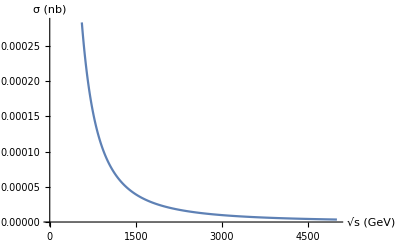

```mathematica
ListPlot[TableCross,Joined->True,AxesLabel-> {"√s (GeV)","σ (nb)"}]
```

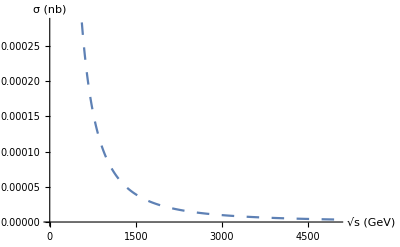

```mathematica
ListPlot[TableCross,Joined->True,AxesLabel-> {"√s  (GeV)","σ (nb)"},PlotStyle->{Dashing[Medium]}]
```

## Plot Cross Section, (up to 1000 GeV)

```mathematica
Qmax=1000.;
Qmin=1.;
Npt=100;
```

```mathematica
TableCross2=Table[{Q[i],σ[Q[i]]},{i,0,Npt}]
```

{{1.,99.4606},{10.99,0.745002},{20.98,0.203378},{30.97,0.0931117},{40.96,0.0531525},{50.95,0.0343162},{60.94,0.0239682},{70.93,0.0176808},{80.92,0.0135775},{90.91,0.0107526},{100.9,0.00872546},{110.89,0.00722169},{120.88,0.00607553},{130.87,0.00518198},{140.86,0.00447193},{150.85,0.00389837},{160.84,0.00342844},{170.83,0.00303861},{180.82,0.00271166},{190.81,0.00243476},{200.8,0.00219819},{210.79,0.00199448},{220.78,0.00181783},{230.77,0.00166364},{240.76,0.00152826},{250.75,0.00140875},{260.74,0.00130273},{270.73,0.00120824},{280.72,0.00112366},{290.71,0.00104767},{300.7,0.000979123},{310.69,0.000917091},{320.68,0.000860771},{330.67,0.000809482},{340.66,0.000762644},{350.65,0.000719755},{360.64,0.000680384},{370.63,0.000644156},{380.62,0.000610746},{390.61,0.000579868},{400.6,0.000551274},{410.59,0.000524743},{420.58,0.000500082},{430.57,0.000477119},{440.56,0.000455701},{450.55,0.000435694},{460.54,0.000416975},{470.53,0.000399437},{480.52,0.000382982},{490.51,0.000367524},{500.5,0.000352982},{510.49,0.000339287},{520.48,0.000326373},{530.47,0.000314182},{540.46,0.000302662},{550.45,0.000291764},{560.44,0.000281444},{570.43,0.000271662},{580.42,0.00026238},{590.41,0.000253567},{600.4,0.00024519},{610.39,0.000237221},{620.38,0.000229635},{630.37,0.000222406},{640.36,0.000215514},{650.35,0.000208937},{660.34,0.000202656},{670.33,0.000196654},{680.32,0.000190915},{690.31,0.000185424},{700.3,0.000180166},{710.29,0.000175128},{720.28,0.000170299},{730.27,0.000165667},{740.26,0.000161221},{750.25,0.000156952},{760.24,0.00015285},{770.23,0.000148906},{780.22,0.000145114},{790.21,0.000141464},{800.2,0.00013795},{810.19,0.000134566},{820.18,0.000131305},{830.17,0.00012816},{840.16,0.000125128},{850.15,0.000122201},{860.14,0.000119376},{870.13,0.000116648},{880.12,0.000114013},{890.11,0.000111465},{900.1,0.000109002},{910.09,0.00010662},{920.08,0.000104315},{930.07,0.000102084},{940.06,0.0000999239},{950.05,0.0000978315},{960.04,0.0000958041},{970.03,0.000093839},{980.02,0.0000919338},{990.01,0.000090086},{1000.,0.0000882934}}

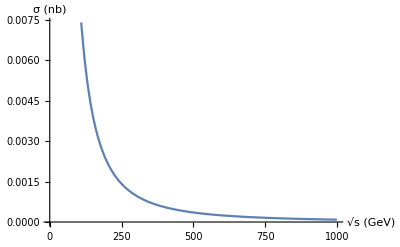

```mathematica
ListPlot[TableCross2,Joined->True,AxesLabel-> {"√s (GeV)","σ (nb)"}]
```

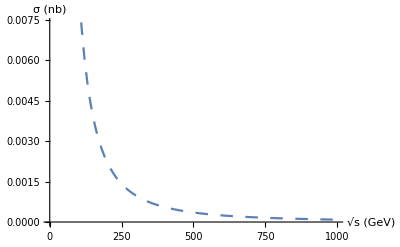

```mathematica
A=ListPlot[TableCross2,Joined->True,AxesLabel-> {"√s  (GeV)","σ (nb)"},PlotStyle->{Dashing[Medium]}]
```

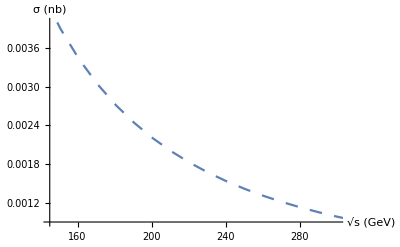

```mathematica
A1=ListPlot[TableCross2,Joined->True,AxesLabel-> {"√s  (GeV)","σ (nb)"},PlotStyle->{Dashing[Medium]},PlotRange->{{145,300},{0.0009,0.004}}]
```

## Plot Born Cross Section (up to 1000 GeV)

```mathematica
σB[Q_]:=Conversion*(4π α^2)/(3Q*Q);
```

```mathematica
TableBorn=Table[{Q[i],σB[Q[i]]},{i,0,Npt}]
```

{{1.,86.8493},{10.99,0.71907},{20.98,0.197313},{30.97,0.0905491},{40.96,0.0517662},{50.95,0.0334563},{60.94,0.0233863},{70.93,0.0172626},{80.92,0.0132634},{90.91,0.0105086},{100.9,0.00853069},{110.89,0.00706288},{120.88,0.00594371},{130.87,0.00507091},{140.86,0.00437715},{150.85,0.00381659},{160.84,0.00335721},{170.83,0.00297604},{180.82,0.00265628},{190.81,0.00238542},{200.8,0.00215397},{210.79,0.00195464},{220.78,0.00178175},{230.77,0.00163083},{240.76,0.0014983},{250.75,0.00138129},{260.74,0.00127747},{270.73,0.00118493},{280.72,0.0011021},{290.71,0.00102765},{300.7,0.000960505},{310.69,0.000899729},{320.68,0.000844545},{330.67,0.000794286},{340.66,0.000748383},{350.65,0.000706348},{360.64,0.000667757},{370.63,0.000632245},{380.62,0.000599492},{390.61,0.000569219},{400.6,0.000541183},{410.59,0.000515169},{420.58,0.000490986},{430.57,0.000468467},{440.56,0.000447462},{450.55,0.000427839},{460.54,0.000409479},{470.53,0.000392276},{480.52,0.000376135},{490.51,0.00036097},{500.5,0.000346704},{510.49,0.000333267},{520.48,0.000320596},{530.47,0.000308635},{540.46,0.00029733},{550.45,0.000286636},{560.44,0.000276508},{570.43,0.000266908},{580.42,0.000257799},{590.41,0.000249149},{600.4,0.000240927},{610.39,0.000233105},{620.38,0.000225658},{630.37,0.000218562},{640.36,0.000211796},{650.35,0.000205339},{660.34,0.000199173},{670.33,0.000193281},{680.32,0.000187646},{690.31,0.000182254},{700.3,0.000177092},{710.29,0.000172145},{720.28,0.000167403},{730.27,0.000162854},{740.26,0.000158489},{750.25,0.000154296},{760.24,0.000150267},{770.23,0.000146395},{780.22,0.00014267},{790.21,0.000139085},{800.2,0.000135634},{810.19,0.00013231},{820.18,0.000129106},{830.17,0.000126018},{840.16,0.000123039},{850.15,0.000120164},{860.14,0.000117389},{870.13,0.000114709},{880.12,0.00011212},{890.11,0.000109617},{900.1,0.000107198},{910.09,0.000104857},{920.08,0.000102592},{930.07,0.0001004},{940.06,0.0000982778},{950.05,0.0000962218},{960.04,0.0000942297},{970.03,0.0000922988},{980.02,0.0000904267},{990.01,0.0000886109},{1000.,0.0000868493}}

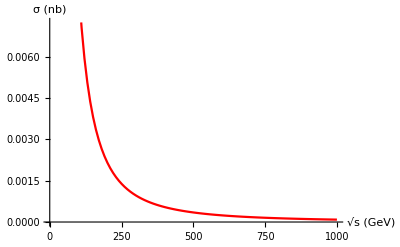

```mathematica
ListPlot[TableBorn,Joined->True,AxesLabel-> {"√s (GeV)","σ (nb)"},PlotStyle->Red]
```

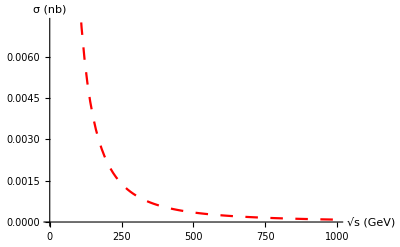

```mathematica
B=ListPlot[TableBorn,Joined->True,AxesLabel-> {"√s  (GeV)","σ (nb)"},PlotStyle->{Dashing[Medium],Red}]
```

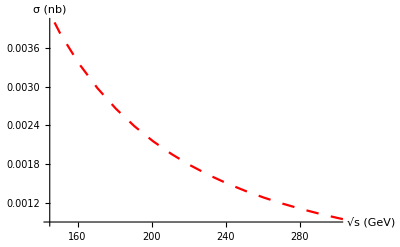

```mathematica
B1=ListPlot[TableBorn,Joined->True,AxesLabel-> {"√s  (GeV)","σ (nb)"},PlotStyle->{Dashing[Medium],Red},PlotRange->{{145,300},{0.0009,0.004}}]
```

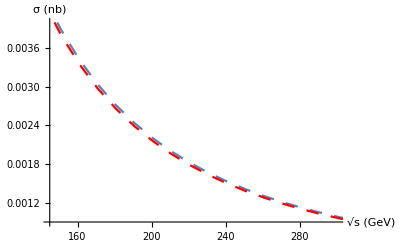

```mathematica
Show[A1,B1]
```

## Overlay Zoom In (Born with 1st Order Correction)

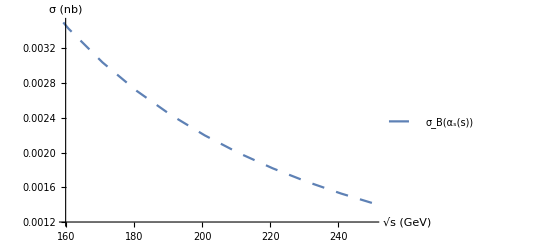

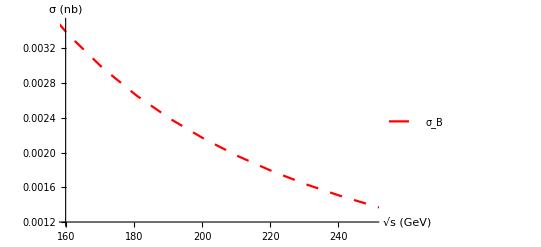

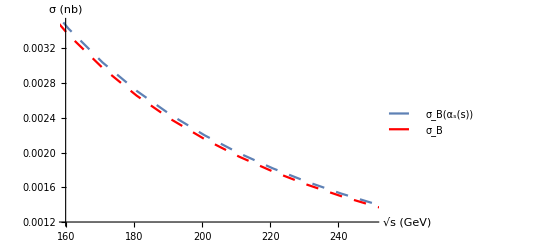

```mathematica
A2=ListPlot[TableCross2,Joined->True,AxesLabel-> {"√s  (GeV)","σ (nb)"},PlotStyle->{Dashing[Medium]},PlotRange->{{160,250},{0.0012,0.0035}},PlotLegends->{"σ_B(α_s(s))"}]
B2=ListPlot[TableBorn,Joined->True,AxesLabel-> {"√s  (GeV)","σ (nb)"},PlotStyle->{Dashing[Medium],Red},PlotRange->{{160,250},{0.0012,0.0035}},PlotLegends->{"σ_B"}]
Show[A2,B2]
```